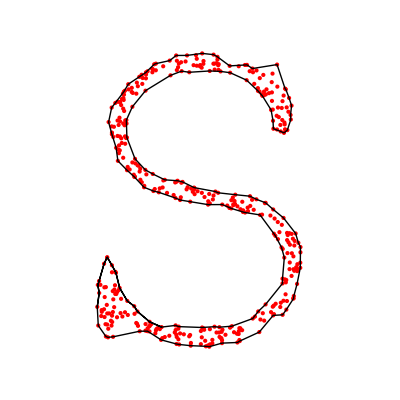

```mathematica
Module[{list,tour,tour1,prev,k1,l,pts,θ,r,newpts,lever,rotatecenter,pointcloud,distances,result,vector,angle,framecenter,center,p,m,dem,prev1},r=10;
SeedRandom[40];list=RandomPoint[DiscretizeGraphics[Text[Style["S",FontFamily->"Courier",300]],_Text],450];
m=ReverseSortBy[list,First][[-1]];k1=RandomInteger[{1,600}];tour=list;
tour1={m,m-{r*0.001,-0.001}};pointcloud=list;

result=tour1;pts=tour1;
l:=Apply[EuclideanDistance,pts];θ:=ArcCos[(l/2)/r];
framecenter:={r*Cos[θ],r*Sin[θ]};
vector:=pts[[2]]-pts[[1]];
angle:=Which[vector[[1]]>0&&vector[[2]]>0,VectorAngle[vector,{1,0}],vector[[1]]<0&&vector[[2]]>0,VectorAngle[vector,{1,0}],vector[[1]]<0&&vector[[2]]<0,2Pi-VectorAngle[vector,{1,0}],vector[[1]]>0&&vector[[2]]<0,2Pi-VectorAngle[vector,{1,0}]];
center:=({{Cos[angle], -Sin[angle]}, {Sin[angle], Cos[angle]}}).framecenter+pts[[1]];
lever:=center-pts[[2]];
rotatecenter[x_,lever_,pts_]:=({{Cos[x], Sin[x]}, {-Sin[x], Cos[x]}}).lever+pts;
Monitor[For[k=1,k<=Length[list],k=k+1,For[i=1,i<=2Pi,i=i+0.08,p=Graphics[{Circle[rotatecenter[i,lever,pts[[2]]],r],Point[rotatecenter[i,lever,pts[[2]]]],{Red,Point[pointcloud]},Line[result]},PlotRange->{{-120,120},{-120,120}}];prev=pts;distances=SortBy[Map[{#,EuclideanDistance[rotatecenter[i,lever,pts[[2]]],#]}&,pointcloud],Last];If[distances[[1]][[2]]<r,AppendTo[result,distances[[1]][[1]]];pts={pts[[2]],distances[[1]][[1]]};Break[]];];If[Length[result]==15,prev1=result[[-5;;-1]]];If[Length[result]>15&&prev1==result[[-5;;-1]],Break[]];Table[If[result[[-y;;-1]]==result[[-2y;;-y-1]],Break[]],{y,2,7,1}];],p];Graphics[{{Red,Point[pointcloud]},Line[result]},PlotRange->{{-100,100},{-100,100}}]]
```